```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

```mathematica
<<init`
```

## Monochromatic

```mathematica
As=5 10^-3;(*10^-2;*)(*3.625 10^-3;*)
```

### direct sampling

```mathematica
npeak=32;
NL=512;
kpeak=2π npeak/NL
σ2=kpeak^2;σ2//N
```

π/8

0.154213

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/mono_Lpeak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/mono_Cpeak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}]
```

{{},{},{},{},{},{},{},{},{},{}}

```mathematica
Select[HighLdata[[2]],250<#[[1]]<270&]
```

{{251,94,507,0.675894,0.39247},{254,173,394,0.679462,0.393136},{255,323,350,0.620138,0.392765},{256,470,56,0.632658,0.393413},{257,201,460,0.811681,0.392782},{257,469,56,0.629589,0.393758},{264,334,399,0.619223,0.39246},{267,108,504,0.618745,0.392397}}

```mathematica
Select[HighLdata[[4]],175<#[[1]]<195&]
```

{{182,102,387,0.656121,0.393635},{187,318,360,0.632321,0.393152}}

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nnu2PT[nu2_]=kpeak^3/(6π)^(3/2) f[nu2] 1/Sqrt[2π] Exp[-nu2^2/2];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

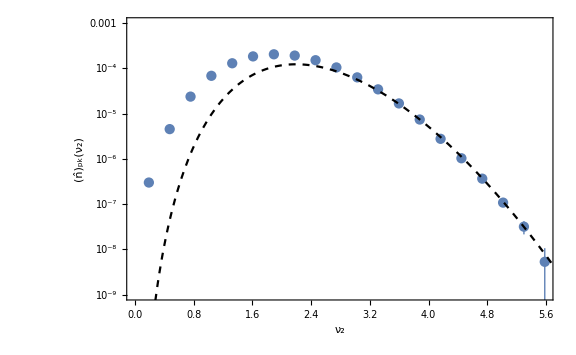

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],"monochromatic"}},PlotRange->{10^-9,10^-3},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.8,0.8}]],
LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.8,0.8}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

```mathematica
nu2inCm[Cm_]=(Sqrt[1-3/2 Cm]-1)/(c Sqrt[As])/.{c->-1.06};
```

```mathematica
nCpt[Cm_]=nnu2PT[nu2inCm[Cm]]nu2inCm'[Cm];
```

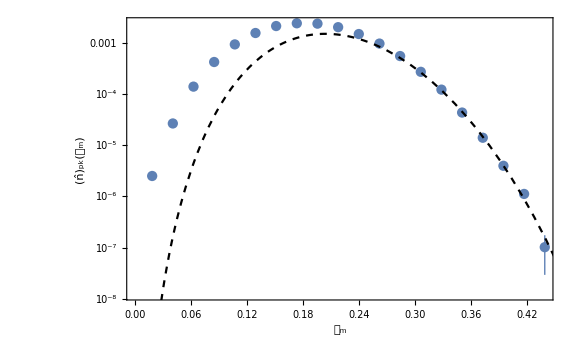

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],"monochromatic"}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCpt[Cm],{Cm,0,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

### Importance Sampling

```mathematica
npeak=16;
NL=256;
kpeak=2π npeak/NL
σ2=kpeak^2;σ2//N
```

π/8

0.154213

```mathematica
ISdata=Drop[Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"],1000];
Ntot=Length[ISdata]
```

1000

```mathematica
Cmdata=Map[{#[[6]],Log10[Exp[#[[7]]]]}&,ISdata];
```

```mathematica
DensityHistogram[Cmdata,ChartLegends->Automatic,FrameLabel->{Subscript[𝒞, "m"],"log_10𝒲"},GridLines->{{0.533},None}]
```

-Graphics-

```mathematica
Dnu2IS=HistogramList[ISdata[[All,2]]/σ2][[1,2]]-HistogramList[ISdata[[All,2]]/σ2][[1,1]]
```

1/2

```mathematica
nu2minIS=HistogramList[ISdata[[All,2]]/σ2][[1,1]]
nu2maxIS=HistogramList[ISdata[[All,2]]/σ2][[1]]//Last
```

5

12

```mathematica
nu2binning[nu2_]:=Select[ISdata,nu2<=(#[[2]])/σ2<nu2+Dnu2IS&]
k33sum[mu2_]:=Total[(nu2binning[mu2][[All,3]])^3]
```

```mathematica
nSnu2List=Table[{nu2+Dnu2IS/2,k33sum[nu2]/(Ntot Dnu2IS)},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
```

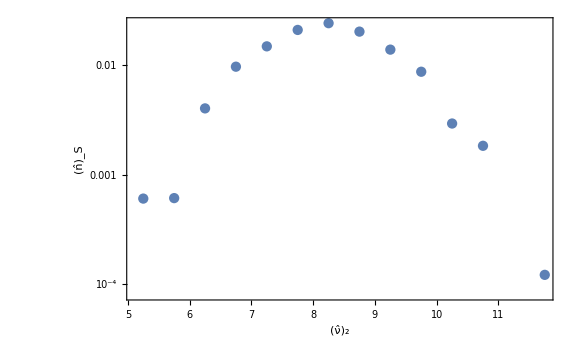

```mathematica
ListLogPlot[nSnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wnu2List=Table[{nu2,If[Length[nu2binning[nu2]]>1,Exp[Mean[nu2binning[nu2][[All,7]]]+Variance[nu2binning[nu2][[All,7]]]/2],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
wnu2errp=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
wnu2errm=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[-Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];;
```

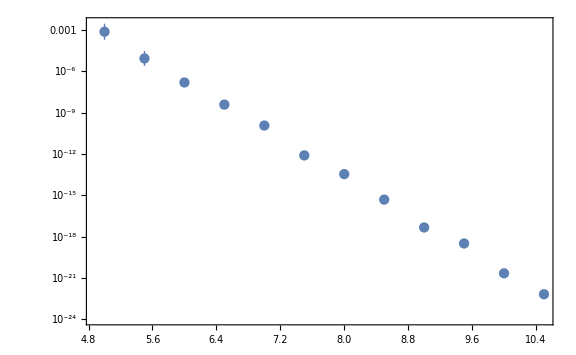

```mathematica
ListLogPlot[Table[{wnu2List[[i,1]],wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[wnu2List]}],Joined->False]
```

```mathematica
nTnu2List=Table[{nSnu2List[[i,1]],nSnu2List[[i,2]]wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[nSnu2List]}];
```

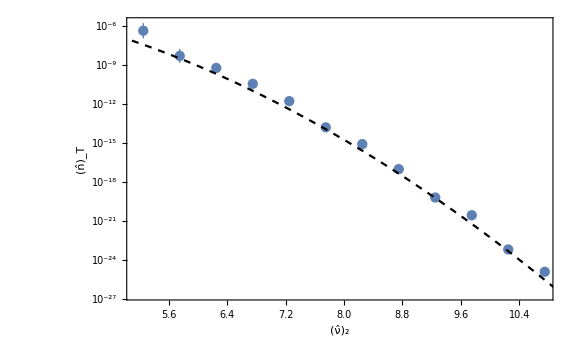

```mathematica
Show[ListLogPlot[nTnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "T"]}],LogPlot[nnu2PT[nu2],{nu2,4,15},PlotStyle->{Black,Dashed}]]
```

```mathematica
padding={{100,10},{70,10}};
```

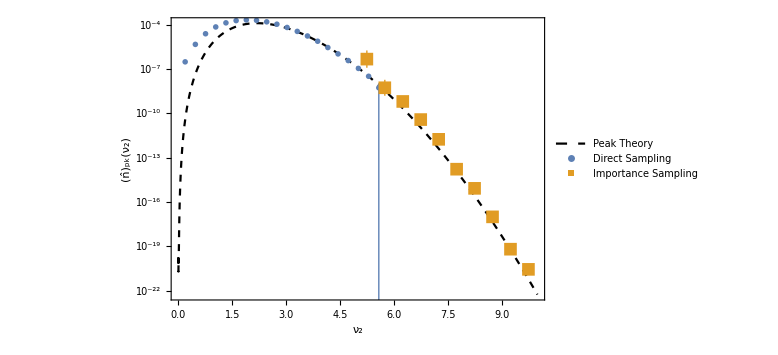

```mathematica
Show[LogPlot[nnu2PT[nu2],{nu2,0,10}(*,PlotRange->{10^-14,10^-2}*),PlotStyle->{Black,Dashed},FrameLabel->{Subscript[ν, 2],Subscript[OverHat[n], pk][Subscript[ν, 2]]},PlotLegends->Placed[LineLegend[{"Peak Theory"},LegendMarkerSize->20,LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.3},Right}],ImagePadding->padding],
ListLogPlot[nnu2Lat,Joined->False,PlotMarkers->Style["●",Color[1]],PlotLegends->Placed[PointLegend[{"Direct Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.2},Right}]],
ListLogPlot[nTnu2List,Joined->False,PlotMarkers->Style["■",Color[2],13],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.1},Right}]]]
```

```mathematica
DCIS=HistogramList[ISdata[[All,6]]][[1,2]]-HistogramList[ISdata[[All,6]]][[1,1]]
```

1/100

```mathematica
CminIS=HistogramList[ISdata[[All,6]]][[1,1]]
CmaxIS=HistogramList[ISdata[[All,6]]][[1]]//Last
```

41/100

33/50

```mathematica
Cbinning[Cm_]:=Select[ISdata,Cm<=#[[6]]<Cm+DCIS&]
k33sumC[Cm_]:=Total[(Cbinning[Cm][[All,3]])^3]
```

```mathematica
nSCList=Table[{Cm+DCIS/2,k33sumC[Cm]/(Ntot DCIS)},{Cm,CminIS,CmaxIS,DCIS}];
```

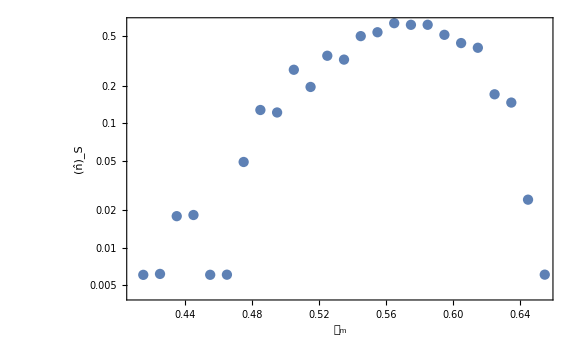

```mathematica
ListLogPlot[nSCList,Joined->False,FrameLabel->{Subscript[𝒞, "m"],Subscript[OverHat[n], "S"]}]
```

```mathematica
wCList=Table[{Cm,If[Length[Cbinning[Cm]]>1,Exp[Mean[Cbinning[Cm][[All,7]]]+Variance[Cbinning[Cm][[All,7]]]/2],0]},{Cm,CminIS,CmaxIS,DCIS}];
wCerrp=Table[{Cm,If[Length[Cbinning[Cm]]>1,Abs[Exp[Sqrt[Variance[Cbinning[Cm][[All,7]]]/Length[Cbinning[Cm]]+Variance[Cbinning[Cm][[All,7]]]^2/(2Length[Cbinning[Cm]]-2)]]-1],0]},{Cm,CminIS,CmaxIS,DCIS}];
wCerrm=Table[{Cm,If[Length[Cbinning[Cm]]>1,Abs[Exp[-Sqrt[Variance[Cbinning[Cm][[All,7]]]/Length[Cbinning[Cm]]+Variance[Cbinning[Cm][[All,7]]]^2/(2Length[Cbinning[Cm]]-2)]]-1],0]},{Cm,CminIS,CmaxIS,DCIS}];
```

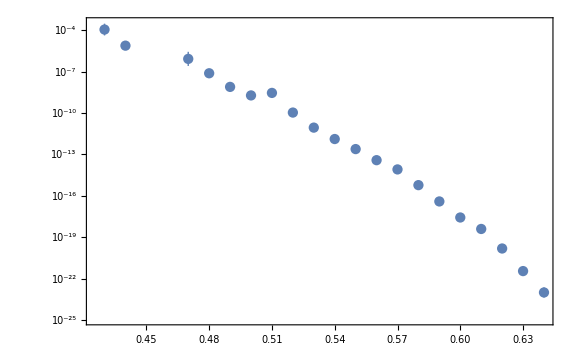

```mathematica
ListLogPlot[Table[{wCList[[i,1]],wCList[[i,2]]Around[1,{wCerrm[[i,2]],wCerrp[[i,2]]}]},{i,Length[wCList]}],Joined->False]
```

```mathematica
nTCList=Table[{nSCList[[i,1]],nSCList[[i,2]]wCList[[i,2]]Around[1,{wCerrm[[i,2]],wCerrp[[i,2]]}]},{i,Length[nSCList]}];
```

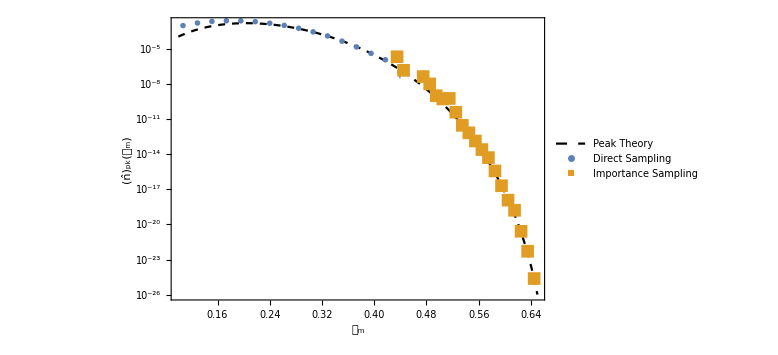

```mathematica
Show[LogPlot[nCpt[Cm],{Cm,0.1,0.65}(*,PlotRange->{10^-15,10^-1}*),PlotStyle->{Black,Dashed},FrameLabel->{Subscript[𝒞, "m"],Subscript[OverHat[n], pk][Subscript[𝒞, "m"]]},PlotLegends->Placed[LineLegend[{"Peak Theory"},LegendMarkerSize->20,LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.3},Right}],ImagePadding->padding],
ListLogPlot[nCLat,Joined->False,PlotMarkers->Style["●",Color[1]],PlotLegends->Placed[PointLegend[{"Direct Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.2},Right}]],
ListLogPlot[nTCList,Joined->False,PlotMarkers->Style["■",Color[2],13],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.1},Right}]]]
```

## Lognormal σ^2=0.01

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-2;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/100) π)

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(1/50)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];]
```

{10.1575,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

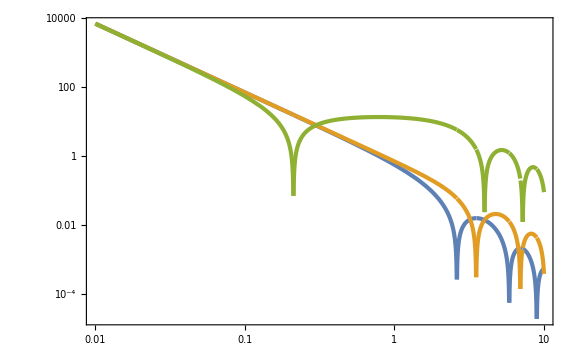

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),1]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

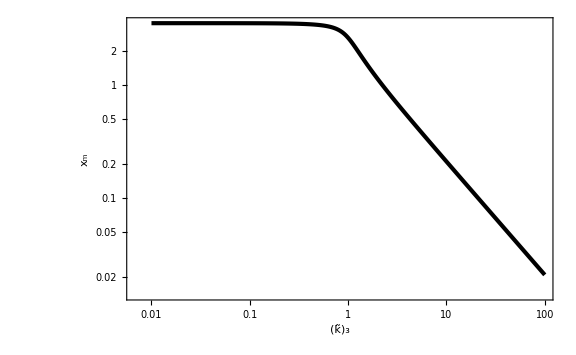

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,5/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

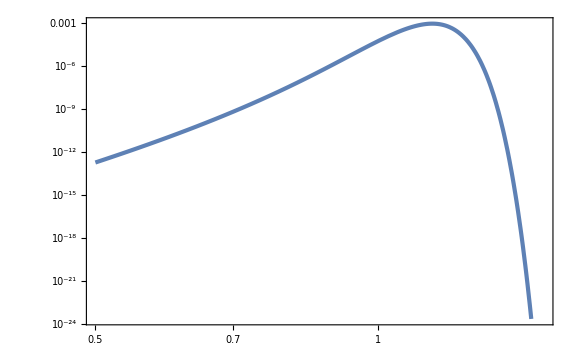

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->1/10},{k3t,5/10,3/2},WorkingPrecision->30]
```

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{117.274,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,01_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,01_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

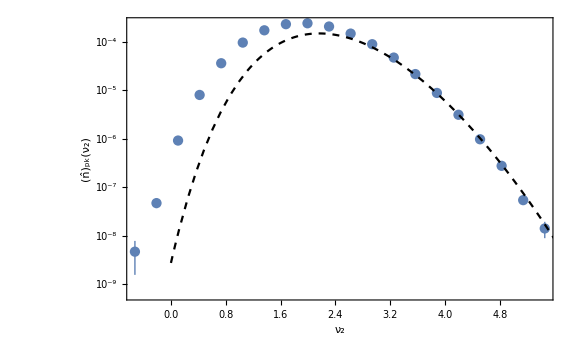

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

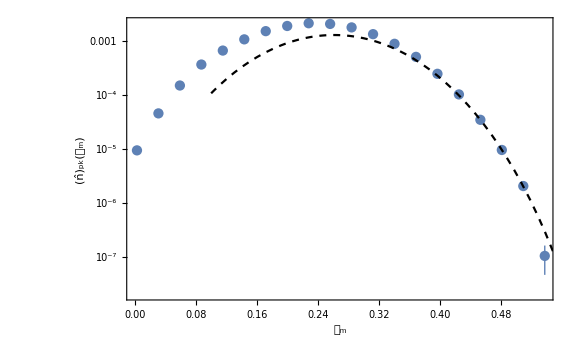

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

## Lognormal σ^2=0.03

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=3/100;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(21/100) π)

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(3/50)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];]
```

{13.5043,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

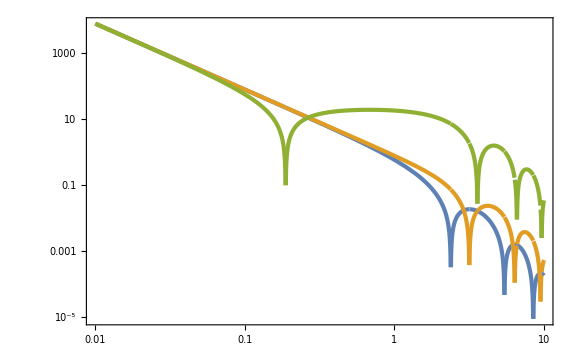

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),1]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

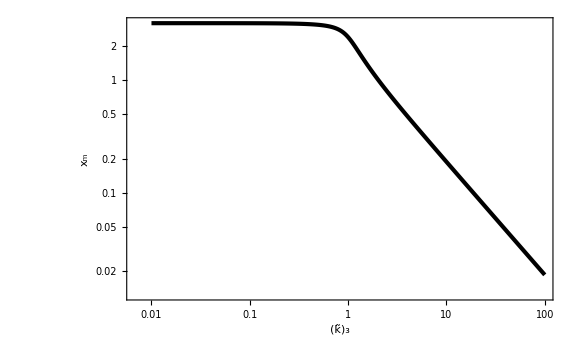

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,5/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

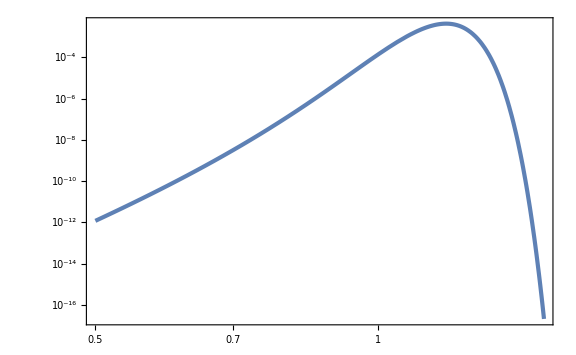

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->1/10},{k3t,5/10,3/2},WorkingPrecision->30]
```

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{123.009,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=1;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,03_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,03_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
(*nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];*)
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)(*±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)*)},{i,nunBins}];
```

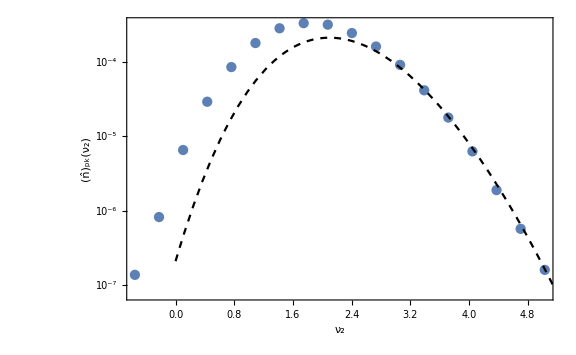

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
(*CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];*)
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)(*±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)*)},{i,CnBins}];
```

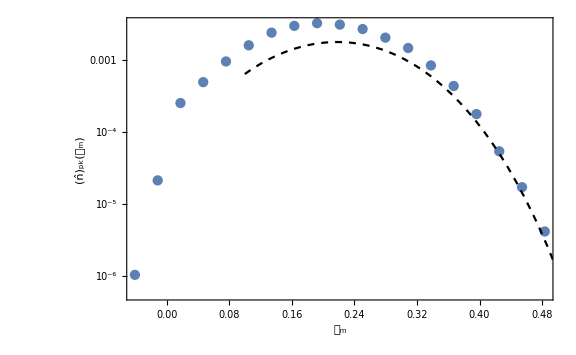

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

## Lognormal σ^2=0.05

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=5/100;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/20) π)

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(1/10)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];]
```

{14.7274,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

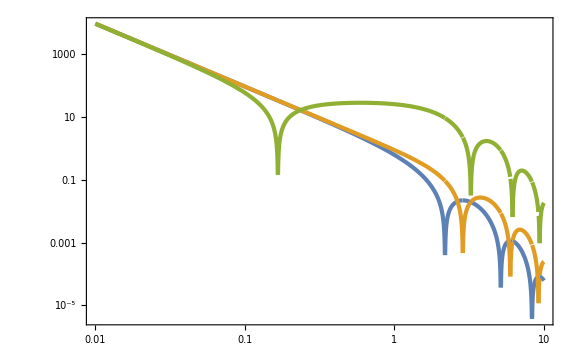

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),1]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

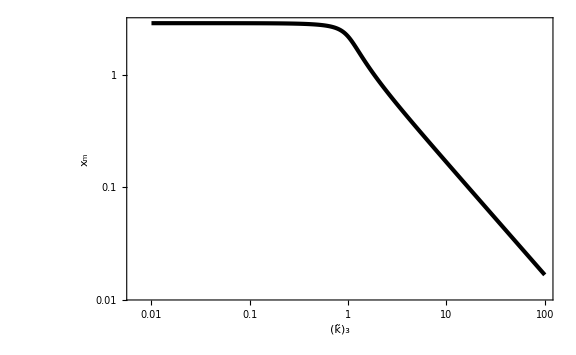

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,5/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

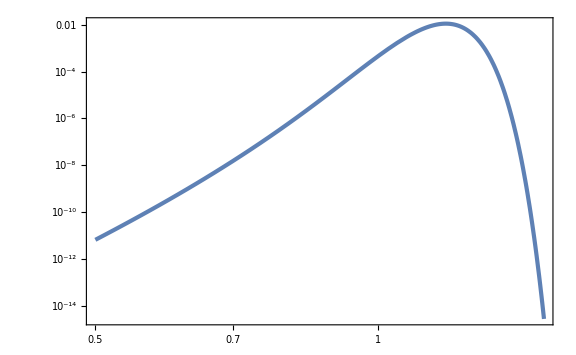

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->1/10},{k3t,5/10,3/2},WorkingPrecision->30]
```

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{124.487,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,05_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,05_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

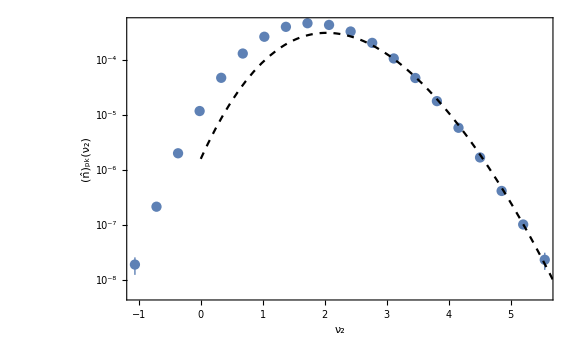

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

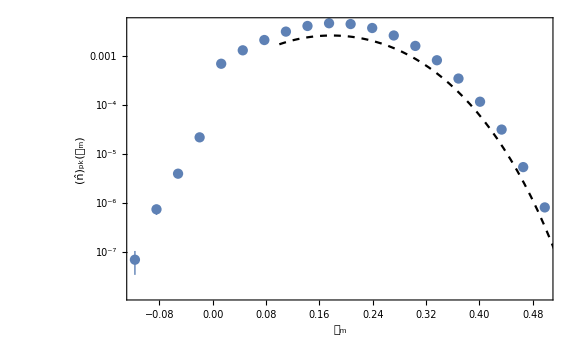

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

## Lognormal σ^2=0.1

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-1;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/10) π)

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(1/5)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];]
```

{21.6894,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

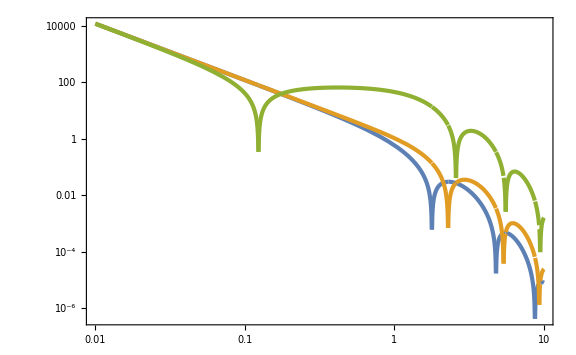

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),1]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

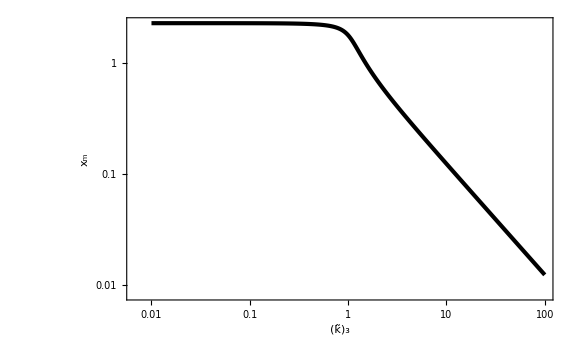

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,5/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

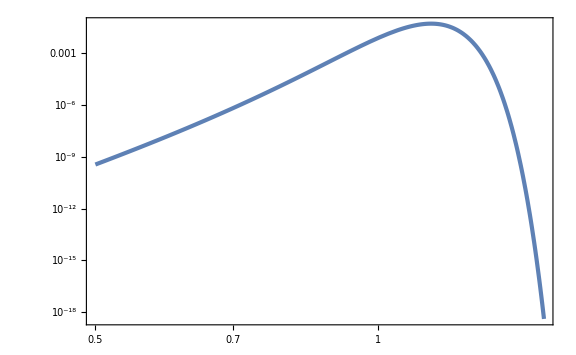

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->1/10},{k3t,5/10,3/2},WorkingPrecision->30]
```

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{115.571,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

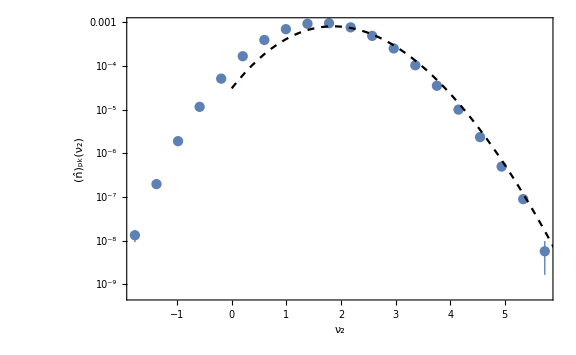

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

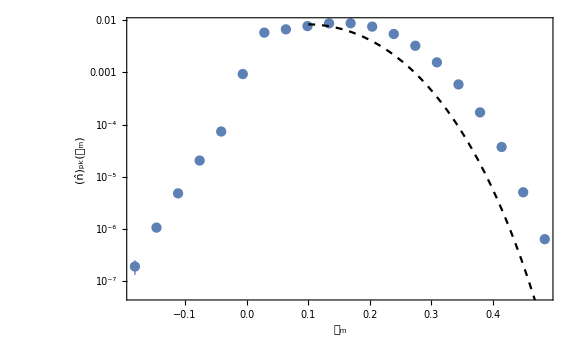

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

## Lognormal σ^2=0.2

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=2 10^-1;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/5) π)

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(2/5)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]//Quiet},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]//Quiet},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]//Quiet},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]//Quiet},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]//Quiet},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]//Quiet},{x,10^-2,10,10^-2}];]
```

{29.8748,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

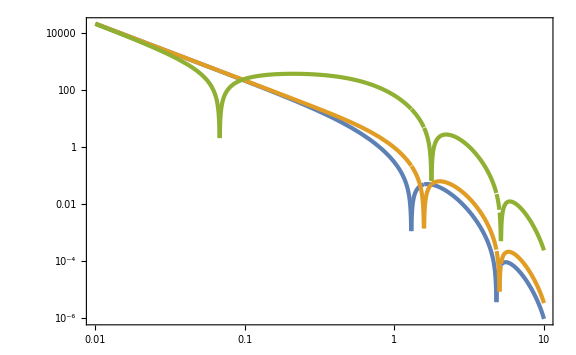

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),0.05]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

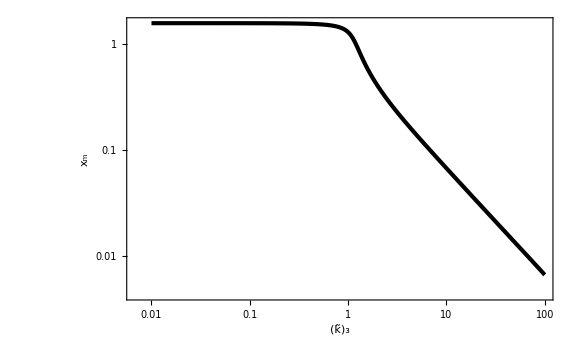

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,1/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

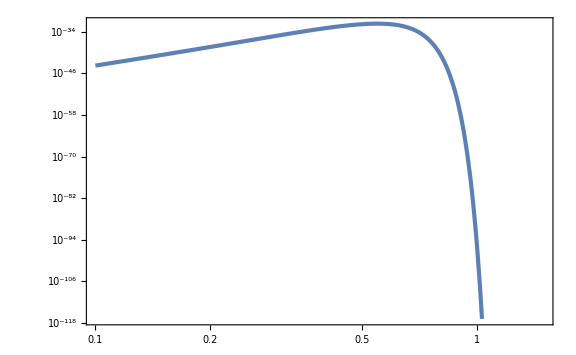

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->6/10},{k3t,1/10,3/2},WorkingPrecision->30]
```

```mathematica
nCpt[5/10]
```

3.24543×10^-18

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{210.572,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,2_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,2_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
HighCdata
```

{{{4,43,421,222,0.461824},{7,488,276,19,0.478991}},{{4,71,272,416,0.451021}},{{4,227,31,72,0.45599}},{{5,478,478,38,0.469243},{5,482,254,80,0.450418},{7,126,4,477,0.466538},{7,468,435,445,0.452097}},{{6,501,2,56,0.453136}},{{5,99,199,325,0.464088},{5,173,327,227,0.457168},{7,223,364,190,0.458006},{8,223,364,189,0.451987}},{{5,383,88,283,0.482896}},{{5,177,2,74,0.459678}},{{5,281,214,50,0.454028},{5,351,302,155,0.461731}},{{4,62,187,235,0.460302},{5,62,187,236,0.470164},{6,227,244,465,0.459463},{8,403,31,208,0.479828},{10,421,373,325,0.456722}}}

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

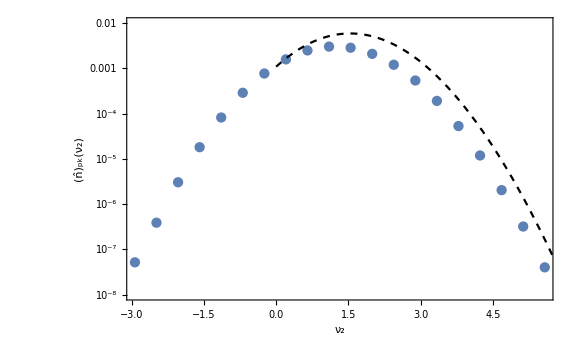

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}},PlotRange->{10^-8,10^-2},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

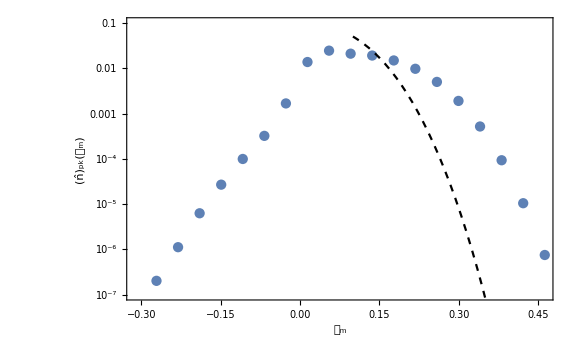

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}],PlotRange->{10^-7,10^-1}],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

## Lognormal σ^2=1

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=1;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^7 π)

```mathematica
γn=E^(-2s2)
```

1/ⅇ^2

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30,MaxRecursion->20]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30,MaxRecursion->20]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30,MaxRecursion->20]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30,MaxRecursion->20]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30,MaxRecursion->20]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30,MaxRecursion->20]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]//Quiet},{x,10^-2,5,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]//Quiet},{x,10^-2,5,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]//Quiet},{x,10^-2,5,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]//Quiet},{x,10^-2,5,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]//Quiet},{x,10^-2,5,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]//Quiet},{x,10^-2,5,10^-2}];]
```

{353.464,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

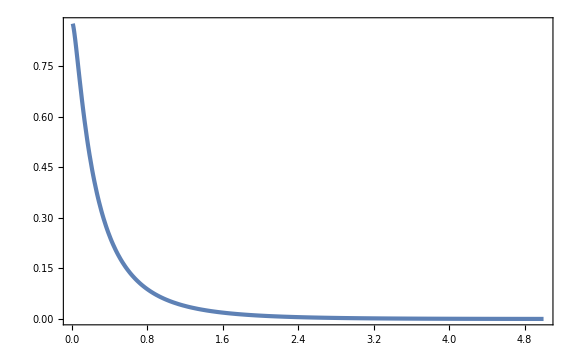

```mathematica
Plot[ζx[x,1],{x,0.01,5},PlotRange->Full]
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

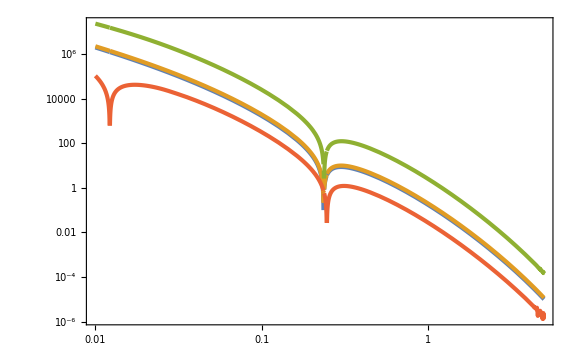

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]],Abs[CmCond[x,2.9]]},{x,10^-2,5}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,(*Min[1/(2 10^lnk3t),0.1]*)0.011},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

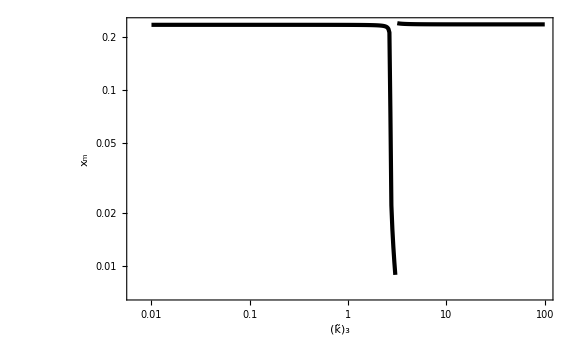

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,1/10,1}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

```mathematica
nCpt[2/10]
```

2.10425×10^-216

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->3/10},{k3t,1/20,1},WorkingPrecision->30]
```

General::munfl: Exp[-1263.45] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1263.46] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
nCpt[1/10]
```

2.09575×10^-46

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{115.571,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=1;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
(*nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];*)
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)(*±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)*)},{i,nunBins}];
```

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

-Graphics-

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
(*CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];*)
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)(*±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)*)},{i,CnBins}];
```

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

-Graphics-

## Lognormal σ^2=0.1 kUV

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-1;
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
```

```mathematica
kUVs=5;
```

```mathematica
AbsoluteTiming[
σ1=Sqrt[kpeak^2 NIntegrate[E^(2 lnk)calPz[lnk],{lnk,-∞,Log[kUVs]}]];
σ2=Sqrt[kpeak^4 NIntegrate[E^(4 lnk)calPz[lnk],{lnk,-∞,Log[kUVs]}]];
σ3=Sqrt[kpeak^6 NIntegrate[E^(6 lnk)calPz[lnk],{lnk,-∞,Log[kUVs]}]];
σ4=Sqrt[kpeak^8 NIntegrate[E^(8 lnk)calPz[lnk],{lnk,-∞,Log[kUVs]}]];
R3=Sqrt[3] σ3/σ4;
γ3=σ3^2/(σ2 σ4);
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,Log[kUVs]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,Log[kUVs]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,Log[kUVs]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,Log[kUVs]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,Log[kUVs]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,Log[kUVs]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ1List=Table[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=Table[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=Table[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=Table[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=Table[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=Table[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
ζx[x_,k3t_]=(1/(1-γ3^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γ3^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γ3^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
xmList=Table[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),0.05]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
xmint[k3t_]=Interpolation[xmList][k3t];
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2^2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,2/5,2}(*,WorkingPrecision->30,MaxRecursion->12*)];
nCptList=Table[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];
]
```

{5676.84,Null}

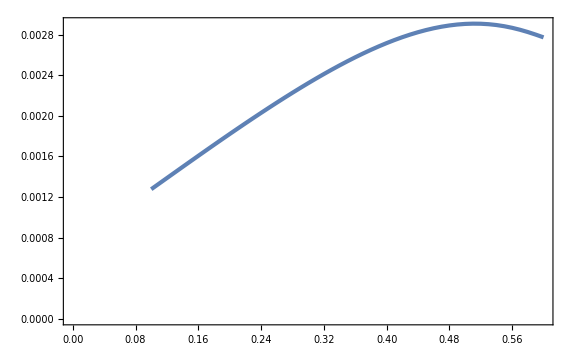

```mathematica
ListPlot[nCptList]
```

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

-Graphics-

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

-Graphics-